```mathematica
(*Mathematica*)
```

```mathematica
(* using the averages as an hidden vacuum point in a fuzzy logic quantum: and numbers instead of bits*)
```

```mathematica
(*adding interpolated true vacuum values:-1/9*)
```

```mathematica
NSolve[1/9==x/1024,x]
```

{{x→113.778}}

```mathematica
v0={0,0.5,1,1.5,2,2.5,3}

u0={413,-(113+7/9),100,256,90,-(113+7/9),421}
```

{0,0.5,1,1.5,2,2.5,3}

{413,-1024/9,100,256,90,-1024/9,421}

```mathematica
Apply[Plus,v0]/7
```

1.5

```mathematica
Apply[Plus,u0]/7
```

9472/63

```mathematica
256/1024
```

1/4

```mathematica
(*Using 2*Sqrt[2] as the true scale of the probabilities*)
```

```mathematica
w=Table[{v0[[i]],u0[[i]]/(2*Sqrt[2]*1024.)},{i,7}]
```

{{0,0.142595},{0.5,-0.0392837},{1,0.0345267},{1.5,0.0883883},{2,0.031074},{2.5,-0.0392837},{3,0.145357}}

```mathematica
(* making the Mexican hat of the Higgs hidden variable*)
```

```mathematica
f[x_]=Fit[w,Table[x^i,{i,0,4}],x]
```

0.142449-0.889781 x+1.38903 x^2-0.729441 x^3+0.121804 x^4

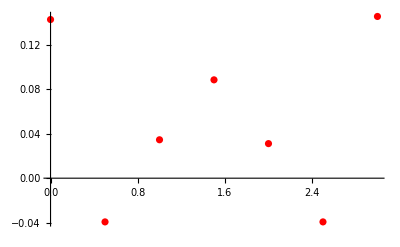

```mathematica
g1=ListPlot[w,PlotStyle->Red, ImageSize->Full]
```

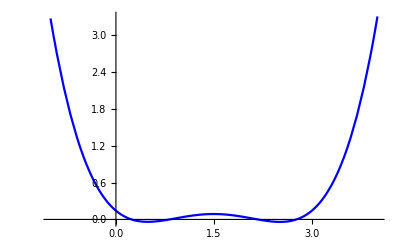

```mathematica
g2=Plot[f[x],{x,-1,4},PlotStyle->Blue, ImageSize->Full,PlotRange->All]
```

```mathematica
(*false vacuum as the average*)
```

```mathematica
f[1.5]
```

0.0878602

```mathematica
%*2*Sqrt[2]
```

0.248506

```mathematica
(*true vacuum states*)
```

```mathematica
f[0.5]
```

-0.0387516

```mathematica
%*2*Sqrt[2]
```

-0.109606

```mathematica
%*1024
```

-112.237

```mathematica
f[2.5]
```

-0.0401327

```mathematica
%*2*Sqrt[2]
```

-0.113512

```mathematica
%*1024
```

-116.237

```mathematica
f[-0.5]
```

1.03339

```mathematica
%*2*Sqrt[2]
```

2.92287

```mathematica
%*1024
```

```mathematica
(2993.01587301589+3033.015873015914)/2
```

3013.02

```mathematica
f[3.5]
```

1.0472

```mathematica
%*2*Sqrt[2]
```

2.96193

```mathematica
%*1024
```

3033.02

```mathematica
(*external bits:-01 and 100*)
```

```mathematica
f[-1.]
```

3.2725

```mathematica
%*2*Sqrt[2]
```

9.25604

```mathematica
%*1024
```

```mathematica
(9478.182539682606+9573.182539682648)/2
```

9525.68

```mathematica
f[4.0]
```

3.3053

```mathematica
%*2*Sqrt[2]
```

9.34881

```mathematica
%*1024
```

9573.18

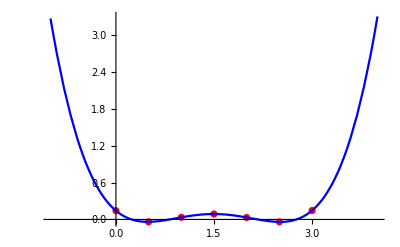

```mathematica
Show[{g1,g2},PlotRange->All]
```

```mathematica
(*end*)
```